Run this quit code if you need to clear all the loaded instances are restart.

```mathematica
Quit
```

# Quantum Resource Estimation - Paper Figure Code

Note: for your best experience, it is advised to run all the code in sequence.

## Part 1: Instantiate Parallelization

First let's set the computation to be parallel:

```mathematica
$ProcessorCount
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->8] (*number of parallelization is set to 8 for a 8-core Mac laptop*)
```

8

ParallelOptions→{AbortPause→2.,BusyWait→0.01,MathLinkTimeout→15.,ParallelThreadNumber→8,RecoveryMode→ReQueue,RelaunchFailedKernels→False,VectorParallelLengthThresholds→{32768,8192,8192,8192}}

## Part 2: Load Packages

This parent notebook is dependent on several functions hosted in the other files . Let' s include them here:

```mathematica
AppendTo[$Path, NotebookDirectory[]];
Needs["BasisGeneration`"];
Needs["CostAnalysis`"];
Needs["SimulationCell`"];
```

Let’s also print out the available pseudo ions here:

```mathematica
Print["Available pseudoions:", HGHData`allElementsNames]
```

Available pseudoions:{C4,N5,O6,Al3,Si4,Fe8,Fe16,Ni10,Ni18,Cu1,Cu11,W6,W14,Ir9,Ir17,Pt10,Pt18,H1,B3,F7,Pd10,Pd18}

## Part 3: Chemical Instances in the Paper

Note: this  part  will  take  significant  amount  of  computing  time  (e . g ., ~1  hour  on  a  Mac  with  M3  chip)

In this part, we run cost estimations for 3 different chemical interaction instances:
a. NH3BF3(instance 1,Lewis acid-base interaction,1 size)
b. DMTM small (instance 2,Direct Methane to Methanol,1 size)
b. DMTM (instance 3,Direct Methane to Methanol,4 sizes)
c. WGS (instance 4,Water Gas Shift,2 sizes)

For all 3 chemical instances (with 7 total sub-instances), we do the following steps
1. construct  the  basis  and  set  the  cell  sizes
2. save basis in present current notebook directory and inspect basis
3. run the QRE process
4. display all the necessary numbers (rescaling factor, block encoding cost, qubit count, and total cost)

!!!Need to test this!!! NOTE: Switch last argument of constructBasis to False if just wanting to observe sim cell and basis data quickly @Karthik which one is this exactly?

### Instance 1: NH_3BF_3

We  first  construct  the  basis  and  set  the  cell  sizes (~91 seconds runtime on M3 mac). We  will  have  G  basis  with  cutoff ~50 Ha  (gives  Λ~10) . We  set ~450 Ha  for  the  ions, so  that  in  general  all  of  the  Λbar >= 30, which  will  be  2 - 4 x  the  electron  cutoff .

```mathematica
(* Construct Basis and Input for Cell: 10x10x15 Angstrom^3. Cutoff: 50,450,1 Ha *)
Instance1Cell=SimulationCell`aVecsRectCuboid[SimulationCell`convertAngstromtoAUCellSpec[{10,10,15}]];
Instance1Basis=EchoTiming@BasisGeneration`constructBasis[Instance1Cell,{50,450,1},True,True]; 
Instance1Input=CostAnalysis`constructInput[<|"N5"->1,"B3"->1 ,"F7"->3,"H1"->3|>,Instance1Basis]

(* Save basis in present current notebook directory and inspect basis *)
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"Instance1Basis.mx"}],Instance1Basis];
BasisGeneration`viewBasisInfo[Instance1Basis]
```

86.3558

{<|N5→1,B3→1,F7→3,H1→3|>,<|Kmax→20.1835,Qmax→40.3669,Kbarmax→82.2138,Qbarmax→164.428,Kbartruncmax→2.81652,Qbartruncmax→5.63304|>}

0.382757

<|nqubits→{6,6,7},nqubitsΛbar→{8,8,9},pmax→{31,31,63},pmaxΛbar→{127,127,255},pmaxΛbartrunc→{5,5,7},cutoff→{{10.3058,10.3058,13.9626},20.1835,203.686,53.1043},cutoffΛbar→{{42.2203,42.2203,56.5154},82.2138,3379.55,891.279},cutoffΛbartrunc→{{1.66222,1.66222,1.5514},2.81652,3.9664,1.20343},Kmax→20.1835,Qmax→40.3669,Kbarmax→82.2138,Qbarmax→164.428,Kbartruncmax→2.81652,Qbartruncmax→5.63304,maxCheck→{True,True},aVecs→{{18.9,0.,0.},{0.,18.9,0.},{0.,0.,28.35}},bVecs→{{0.332444,0.,0.},{0.,0.332444,0.},{0.,0.,0.221629}},basisSize→504063,basistruncSize→1814|>

We can see that for NH3BF3, we put in one N atom (with 5 valence electrons), one B atom (with 1 valence electron), three F atoms (with 7 valence electrons each), and three H atoms (with 1 valence electron each).
Once the basis cutoff is set to the current value, for electron we will need 6 qubits to host information for the x direction, 6 for the y direction, and 7 for the z direction. For ions we will need 8 qubits to host information for the x direction, 8 for the y direction, and 9 for the z direction.
@Karthik maybe add a little more explanations for other values?

With the basis info all set up, we now begin to run the full quantum resource estimation computation (~86 seconds on M3 Mac)

```mathematica
(*Run QRE*)
Instance1Result=EchoTiming@CostAnalysis`fullBlockEncodingCost[Instance1Input,Instance1Basis,True];
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"Instance1Result.mx"}],Instance1Result];
```

86.8443

0.010694

After the QRE calculation is finished, let’s display the result with a time parameter t and a accuracy parameter ϵ (@Karthik can we sync the letters here with the paper?):

```mathematica
(* View Results *)
CostAnalysis`viewAllResults[Instance1Result,t,ϵ] ;
```

Particle Count:<|ηel→32,ηion→8,η→40|>

Rescaling Factors:{,}

Compilation Cost:{{3424,8010,11363,1140,161234},185171}

Qubit Cost:808

Time Evolution Cost:

First, the “particle count” shows that we are considering 32 electrons (5 x 1 + 3 x 1 + 7 x 3 + 1 x 3 = 32), 8 ions (1 + 1 + 3 + 3 = 8), and 40 total charged particles (32 + 8 = 40).

Next, we can see the “rescaling factors” for each part of the Hamiltonian (Tel and Tion are the kinetic terms for electrons and ions, Vel and Vion are the Coulomb interaction terms for electrons and ions, Loc and NL are the local and non-local terms). In the right table, the first row shows the exact rescaling factors for each terms. The second row shows the approximated rescaling factor numbers using theoretical bound we derived in the paper (see Appendix D). The third row shows the difference between the two. (@Karthik maybe you can add a little more setences explaining the left table?)

The “Compilation Cost” shows the required number of Toffoli gates for each terms to complete a single block encoding of the Hamiltonian, with a total sum at the end (in this case 185171 Toffoli gates)

Next we have the logical qubit cost. Note that this is the system qubit numbers required to set up all the wavefunction encodings. We will also require some additional ancilla qubits that scales at most linearly to the number of system qubits. (Need to check this statement with @Sam)

Lastly, we have the exact and theoretically bounded time evolution cost. The “query” column shows the number of walk operators we need to perform, essentially the number of block encodings, as a function of t and ϵ. The “compilation” column shows the Toffoli gate cost for one single block encoding. Multiplying them together, we obtain the “total” Toffoli gate costs at the 3rd column.

### Instance 2: DMTM Small

Now we repeat the same process as we have done for the NH_3BF_3 instance:

```mathematica
(* Construct Basis and Input for Cell: 17x17x17 Angstrom^3. Cutoff: 50,450,1 Ha *)
Instance2Cell=SimulationCell`aVecsRectCuboid[SimulationCell`convertAngstromtoAUCellSpec[{17,17,17}]];
Instance2Basis=EchoTiming@BasisGeneration`constructBasis[Instance2Cell,{50,450,1},True,True]; 
Instance2Input=CostAnalysis`constructInput[<|"N5"->3,"Pd18"->1 ,"C4"->1,"O6"->1,"H1"->10|>,Instance2Basis]

(* Save basis in present current notebook directory and inspect basis *)
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"Instance2Basis.mx"}],Instance2Basis];
BasisGeneration`viewBasisInfo[Instance2Basis]
```

352.892

{<|N5→3,Pd18→1,C4→1,O6→1,H1→10|>,<|Kmax→21.3388,Qmax→42.6776,Kbarmax→86.3714,Qbarmax→172.743,Kbartruncmax→2.70969,Qbartruncmax→5.41938|>}

1.56922

<|nqubits→{7,7,7},nqubitsΛbar→{9,9,9},pmax→{63,63,63},pmaxΛbar→{255,255,255},pmaxΛbartrunc→{8,8,8},cutoff→{{12.32,12.32,12.32},21.3388,227.673,75.8908},cutoffΛbar→{{49.8666,49.8666,49.8666},86.3714,3730.01,1243.34},cutoffΛbartrunc→{{1.56444,1.56444,1.56444},2.70969,3.67121,1.22374},Kmax→21.3388,Qmax→42.6776,Kbarmax→86.3714,Qbarmax→172.743,Kbartruncmax→2.70969,Qbartruncmax→5.41938,maxCheck→{True,True},aVecs→{{32.13,0.,0.},{0.,32.13,0.},{0.,0.,32.13}},bVecs→{{0.195555,0.,0.},{0.,0.195555,0.},{0.,0.,0.195555}},basisSize→2048383,basistruncSize→4912|>

```mathematica
(* Run QRE *)
Instance2Result=EchoTiming@CostAnalysis`fullBlockEncodingCost[Instance2Input,Instance2Basis,True];
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"Instance2Result.mx"}],Instance2Result];
```

599.647

0.010562

```mathematica
(* View Results *)
CostAnalysis`viewAllResults[Instance2Result,t,ϵ]
```

Particle Count:<|ηel→53,ηion→16,η→69|>

Rescaling Factors:{,}

Compilation Cost:{{6488,8992,13172,1400,178848},208900}

Qubit Cost:1545

Time Evolution Cost:

### Instance Class 3: DMTM

Repeat the same process as we have done for the NH_3BF_3 and DMTM small instance, but this time with 3 sub instance with different DMTM sizes:

```mathematica
(* Construct Cell for different sizes n x n lattice of h-BN, 1 Pd-O, 1 CH4 *)
DMTMExtendedCellSpec[n_]:={2.5 n,2.5 n,20};
constructDMTMInputPart[n_]:=<|"B3"->n^2-1,"N5"->n^2 ,"C4"->1,"O6"->1,"H1"->4,"Pd18"->1|>

realSpaceCellSpecDMTMClass=Table[SimulationCell`convertAngstromtoAUCellSpec[DMTMExtendedCellSpec[n]],{n,1,9}];
InstanceCellDMTMClass=Map[SimulationCell`aVecsInPlane120deg,realSpaceCellSpecDMTMClass];

(* Construct Basis and Input for n=3,5,9 as representative cases of interest *)
InstanceBasisDMTMClass3=EchoTiming@BasisGeneration`constructBasis[InstanceCellDMTMClass[[3]],{50,450,1},True,True]; 
InstanceBasisDMTMClass5=EchoTiming@BasisGeneration`constructBasis[InstanceCellDMTMClass[[5]],{30,450,1},True,True]; 
InstanceBasisDMTMClass9=EchoTiming@BasisGeneration`constructBasis[InstanceCellDMTMClass[[9]],{50,450,1},True,True]; 

InstanceInputDMTMClass3=CostAnalysis`constructInput[constructDMTMInputPart[3],InstanceBasisDMTMClass3]
InstanceInputDMTMClass5=CostAnalysis`constructInput[constructDMTMInputPart[5],InstanceBasisDMTMClass5]
InstanceInputDMTMClass9=CostAnalysis`constructInput[constructDMTMInputPart[9],InstanceBasisDMTMClass9]

(* Save basis in present current notebook directory and inspect basis *)
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceBasisDMTMClass3.mx"}],InstanceBasisDMTMClass3];
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceBasisDMTMClass5.mx"}],InstanceBasisDMTMClass5];
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceBasisDMTMClass9.mx"}],InstanceBasisDMTMClass9];
BasisGeneration`viewBasisInfo[InstanceBasisDMTMClass3]
BasisGeneration`viewBasisInfo[InstanceBasisDMTMClass5]
BasisGeneration`viewBasisInfo[InstanceBasisDMTMClass9]
```

82.5098

81.7019

352.419

{<|B3→8,N5→9,C4→1,O6→1,H1→4,Pd18→1|>,<|Kmax→29.4096,Qmax→58.8192,Kbarmax→70.1135,Qbarmax→140.227,Kbartruncmax→3.05143,Qbartruncmax→6.10285|>}

{<|B3→24,N5→25,C4→1,O6→1,H1→4,Pd18→1|>,<|Kmax→19.5335,Qmax→39.0669,Kbarmax→79.7494,Qbarmax→159.499,Kbartruncmax→3.05143,Qbartruncmax→6.10285|>}

{<|B3→80,N5→81,C4→1,O6→1,H1→4,Pd18→1|>,<|Kmax→21.36,Qmax→42.72,Kbarmax→86.4571,Qbarmax→172.914,Kbartruncmax→3.05143,Qbartruncmax→6.10285|>}

0.497955

0.471183

2.42137

<|nqubits→{6,6,7},nqubitsΛbar→{7,7,9},pmax→{31,31,63},pmaxΛbar→{63,63,255},pmaxΛbartrunc→{3,3,9},cutoff→{{15.8667,15.8667,10.472},24.7623,306.585,54.8311},cutoffΛbar→{{32.2453,32.2453,42.3866},62.2587,1938.07,519.88},cutoffΛbartrunc→{{1.53549,1.53549,1.496},2.63694,3.47674,1.119},Kmax→29.4096,Qmax→58.8192,Kbarmax→70.1135,Qbarmax→140.227,Kbartruncmax→3.05143,Qbartruncmax→6.10285,maxCheck→{True,True},aVecs→{{14.175,0.,0.},{-7.0875,12.2759,0.},{0.,0.,37.8}},bVecs→{{0.443258,0.255915,0.},{0.,0.511831,0.},{0.,0.,0.166222}},basisSize→504063,basistruncSize→930|>

<|nqubits→{6,6,7},nqubitsΛbar→{8,8,9},pmax→{31,31,63},pmaxΛbar→{127,127,255},pmaxΛbartrunc→{5,5,9},cutoff→{{9.52005,9.52005,10.472},17.0565,145.462,45.3157},cutoffΛbar→{{39.0015,39.0015,42.3866},69.5619,2419.43,760.558},cutoffΛbartrunc→{{1.53549,1.53549,1.496},2.63694,3.47674,1.119},Kmax→19.5335,Qmax→39.0669,Kbarmax→79.7494,Qbarmax→159.499,Kbartruncmax→3.05143,Qbartruncmax→6.10285,maxCheck→{True,True},aVecs→{{23.625,0.,0.},{-11.8125,20.4599,0.},{0.,0.,37.8}},bVecs→{{0.265955,0.153549,0.},{0.,0.307098,0.},{0.,0.,0.166222}},basisSize→504063,basistruncSize→2298|>

<|nqubits→{7,7,7},nqubitsΛbar→{9,9,9},pmax→{63,63,63},pmaxΛbar→{255,255,255},pmaxΛbartrunc→{9,9,9},cutoff→{{10.7484,10.7484,10.472},18.4586,170.36,54.8311},cutoffΛbar→{{43.5056,43.5056,42.3866},74.7134,2791.05,898.311},cutoffΛbartrunc→{{1.53549,1.53549,1.496},2.63694,3.47674,1.119},Kmax→21.36,Qmax→42.72,Kbarmax→86.4571,Qbarmax→172.914,Kbartruncmax→3.05143,Qbartruncmax→6.10285,maxCheck→{True,True},aVecs→{{42.525,0.,0.},{-21.2625,36.8277,0.},{0.,0.,37.8}},bVecs→{{0.147753,0.0853051,0.},{0.,0.17061,0.},{0.,0.,0.166222}},basisSize→2048383,basistruncSize→6858|>

```mathematica
(* Run QRE *)
InstanceDMTMClass3Result=EchoTiming@CostAnalysis`fullBlockEncodingCost[InstanceInputDMTMClass3,InstanceBasisDMTMClass3,True];
InstanceDMTMClass5Result=EchoTiming@CostAnalysis`fullBlockEncodingCost[InstanceInputDMTMClass5,InstanceBasisDMTMClass5,True];
InstanceDMTMClass9Result=EchoTiming@CostAnalysis`fullBlockEncodingCost[InstanceInputDMTMClass9,InstanceBasisDMTMClass9,True];

EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceDMTMClass3Result.mx"}],InstanceDMTMClass3Result];
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceDMTMClass5Result.mx"}],InstanceDMTMClass5Result];
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceDMTMClass9Result.mx"}],InstanceDMTMClass9Result];
```

127.164

127.618

827.472

0.054632

0.01581

0.008893

```mathematica
(* View Results *)
viewAllResults[InstanceDMTMClass3Result,t,ϵ]
```

```mathematica
viewAllResults[InstanceDMTMClass5Result,t,ϵ]
```

```mathematica
viewAllResults[InstanceDMTMClass9Result,t,ϵ]
```

Particle Count:<|ηel→101,ηion→24,η→125|>

Rescaling Factors:{,}

Compilation Cost:{{10416,7136,10846,1578,161314},191290}

Qubit Cost:2471

Time Evolution Cost:

Particle Count:<|ηel→229,ηion→56,η→285|>

Rescaling Factors:{,}

Compilation Cost:{{24176,8094,12671,1622,161350},207913}

Qubit Cost:5751

Time Evolution Cost:

Particle Count:<|ηel→677,ηion→168,η→845|>

Rescaling Factors:{,}

Compilation Cost:{{78424,9076,17054,1694,179030},285278}

Qubit Cost:18753

Time Evolution Cost:

### Instance Class 4: WGS

Repeat the same process as we have done for all the previous 3 instances, this time for WGS (with 2 sub instance of different sizes):

```mathematica
(* Construct Cell for bilayer (m=2) Cu(100) with m x n x n slab, 1 CO, 1 H2O *)
WGSExtendedCellSpec[n_,m_]:={3.615m+15,3.615 n,3.615 n};
constructWGSInputPart[n_,m_]:=<|"Cu1"->(4m+2) n^2-5,"Cu11"->5 ,"C4"->1,"O6"->2,"H1"->2|>

realSpaceCellSpecWGSClass=Table[SimulationCell`convertAngstromtoAUCellSpec[WGSExtendedCellSpec[n,2]],{n,1,6}];
InstanceCellWGSClass=Map[SimulationCell`aVecsRectCuboid,realSpaceCellSpecWGSClass];
```

```mathematica
(* Construct Basis and Input for bilayer n=3,5 as representative cases of interest *)
InstanceBasisWGSClass3=EchoTiming@BasisGeneration`constructBasis[InstanceCellWGSClass[[3]],{40,450,1},True,True];
InstanceBasisWGSClass5=EchoTiming@BasisGeneration`constructBasis[InstanceCellWGSClass[[5]],{40,450,1},True,True];
```

81.9351

350.799

```mathematica
InstanceInputWGSClass3=CostAnalysis`constructInput[constructWGSInputPart[3,2],InstanceBasisWGSClass3]
InstanceInputWGSClass5=CostAnalysis`constructInput[constructWGSInputPart[5,2],InstanceBasisWGSClass5]
```

{<|Cu1→85,Cu11→5,C4→1,O6→2,H1→2|>,<|Kmax→16.4125,Qmax→32.825,Kbarmax→66.9735,Qbarmax→133.947,Kbartruncmax→2.6334,Qbartruncmax→5.2668|>}

{<|Cu1→245,Cu11→5,C4→1,O6→2,H1→2|>,<|Kmax→18.9022,Qmax→37.8044,Kbarmax→76.5089,Qbarmax→153.018,Kbartruncmax→2.56251,Qbartruncmax→5.12502|>}

```mathematica
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceBasisWGSClass3.mx"}],InstanceBasisWGSClass3];
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceBasisWGSClass5.mx"}],InstanceBasisWGSClass5];
BasisGeneration`viewBasisInfo[InstanceBasisWGSClass3]
BasisGeneration`viewBasisInfo[InstanceBasisWGSClass5]
```

0.463399

1.91935

<|nqubits→{7,6,6},nqubitsΛbar→{9,8,8},pmax→{63,31,31},pmaxΛbar→{255,127,127},pmaxΛbartrunc→{10,5,5},cutoff→{{9.42148,9.50277,9.50277},16.4125,134.685,44.3821},cutoffΛbar→{{38.1346,38.9307,38.9307},66.9735,2242.72,727.122},cutoffΛbartrunc→{{1.49547,1.5327,1.5327},2.6334,3.4674,1.11822},Kmax→16.4125,Qmax→32.825,Kbarmax→66.9735,Qbarmax→133.947,Kbartruncmax→2.6334,Qbartruncmax→5.2668,maxCheck→{True,True},aVecs→{{42.0147,0.,0.},{0.,20.4971,0.},{0.,0.,20.4971}},bVecs→{{0.149547,0.,0.},{0.,0.306541,0.},{0.,0.,0.306541}},basisSize→504063,basistruncSize→2540|>

<|nqubits→{7,7,7},nqubitsΛbar→{9,9,9},pmax→{63,63,63},pmaxΛbar→{255,255,255},pmaxΛbartrunc→{10,8,8},cutoff→{{9.42148,11.5872,11.5872},18.9022,178.646,44.3821},cutoffΛbar→{{38.1346,46.9008,46.9008},76.5089,2926.8,727.122},cutoffΛbartrunc→{{1.49547,1.4714,1.4714},2.56251,3.28323,1.0825},Kmax→18.9022,Qmax→37.8044,Kbarmax→76.5089,Qbarmax→153.018,Kbartruncmax→2.56251,Qbartruncmax→5.12502,maxCheck→{True,True},aVecs→{{42.0147,0.,0.},{0.,34.1618,0.},{0.,0.,34.1618}},bVecs→{{0.149547,0.,0.},{0.,0.183925,0.},{0.,0.,0.183925}},basisSize→2048383,basistruncSize→6068|>

```mathematica
(* Run QRE *)
InstanceWGSClass3Result=EchoTiming@CostAnalysis`fullBlockEncodingCost[InstanceInputWGSClass3,InstanceBasisWGSClass3,True];
InstanceWGSClass5Result=EchoTiming@CostAnalysis`fullBlockEncodingCost[InstanceInputWGSClass5,InstanceBasisWGSClass5,True];
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceWGSClass3Result.mx"}],InstanceWGSClass3Result];
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceWGSClass5Result.mx"}],InstanceWGSClass5Result];
```

112.323

665.592

0.009102

0.005511

```mathematica
(* View Results *)
viewAllResults[InstanceWGSClass3Result,t,ϵ]
```

```mathematica
viewAllResults[InstanceWGSClass5Result,t,ϵ]
```

Particle Count:<|ηel→158,ηion→95,η→253|>

Rescaling Factors:{,}

Compilation Cost:{{22552,8066,12215,1454,161359},205646}

Qubit Cost:5377

Time Evolution Cost:

Particle Count:<|ηel→318,ηion→255,η→573|>

Rescaling Factors:{,}

Compilation Cost:{{56576,9076,14888,1498,179087},261125}

Qubit Cost:13563

Time Evolution Cost:

## Part 4: Data Analysis and Visualization of Instance Results

After computing the QRE for all the instances, we are now ready to visualize all the costs together!

If you have execute all the previous code, you should have obtained a collection of .mx files storing all the QRE results in the local directory. You can uncomment the code below to easily retrieve them if needed.

```mathematica
(* Load data from QRE runs above if not in kernel already *)
(*Get[FileNameJoin[{NotebookDirectory[],"Instance1Result.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"Instance2Result.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceDMTMClass3Result.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceDMTMClass5Result.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceDMTMClass9Result.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceWGSClass3Result.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceWGSClass5Result.mx"}]];*)

(*Get[FileNameJoin[{NotebookDirectory[],"Instance1Basis.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"Instance2Basis.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceBasisDMTMClass3.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceBasisDMTMClass5.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceBasisDMTMClass9.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceBasisWGSClass3.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceBasisWGSClass5.mx"}]];*)
```

### Figure 6 : Normalized Distribution of Rescaling Factors for Each Problem Instance

We first plot the rescaling factors for different chemical instances across all terms in the corresponding Hamiltonians.

True

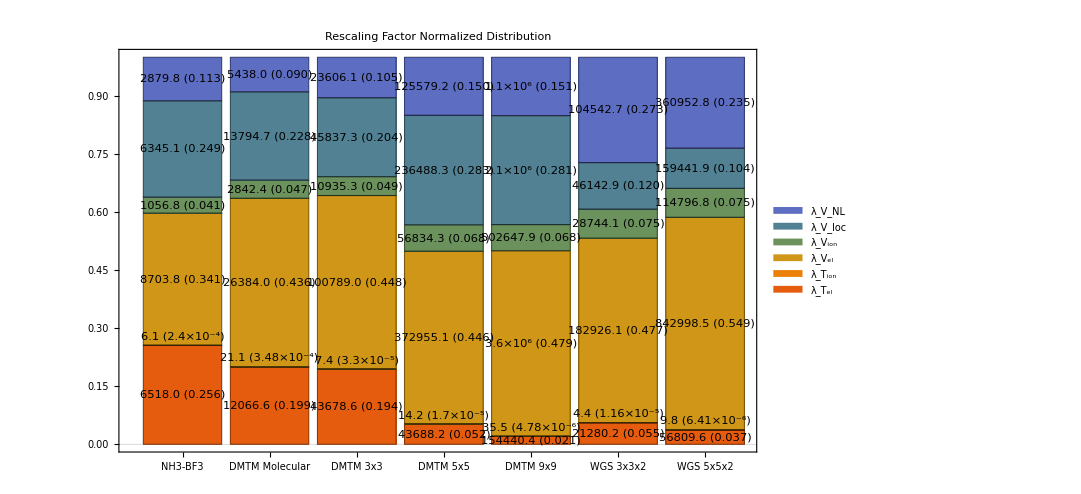

```mathematica
(* Get scaling factor data from all instance results we computed before*)
dataNH3BF3={Instance1Result["exact"]["λTermExact"],Instance1Result["bound"]["λTermBound"]};
dataDMTMSmall={Instance2Result["exact"]["λTermExact"],Instance2Result["bound"]["λTermBound"]};
dataDMTM3={InstanceDMTMClass3Result["exact"]["λTermExact"],InstanceDMTMClass3Result["bound"]["λTermBound"]};
dataDMTM5={InstanceDMTMClass5Result["exact"]["λTermExact"],InstanceDMTMClass5Result["bound"]["λTermBound"]};
dataDMTM9={InstanceDMTMClass9Result["exact"]["λTermExact"],InstanceDMTMClass9Result["bound"]["λTermBound"]};
dataWGS3={InstanceWGSClass3Result["exact"]["λTermExact"],InstanceWGSClass3Result["bound"]["λTermBound"]};
dataWGS5={InstanceWGSClass5Result["exact"]["λTermExact"],InstanceWGSClass5Result["bound"]["λTermBound"]};

allTermData={dataNH3BF3,dataDMTMSmall,dataDMTM3,dataDMTM5,dataDMTM9,dataWGS3,dataWGS5};
exactTermData=First/@allTermData;

totalExactData={Instance1Result["exact"]["λExact"],Instance2Result["exact"]["λExact"],InstanceDMTMClass3Result["exact"]["λExact"],InstanceDMTMClass5Result["exact"]["λExact"],InstanceDMTMClass9Result["exact"]["λExact"],InstanceWGSClass3Result["exact"]["λExact"],InstanceWGSClass5Result["exact"]["λExact"]};

(* Check total rescaling from term based rescaling are all correct *)
checkSum=(Total/@Values/@exactTermData);
totalExactData==checkSum

(* Create figure *)
rescalingFactorDistBarChart=BarChart[Normalize[#,Total]&/@Values/@exactTermData,
ChartLayout->"Stacked",Axes->False,Frame->True,PlotLabel->"Rescaling Factor Normalized Distribution",
ChartLegends->{Style[Subscript["λ",Subscript["T","el"]],14,FontFamily->"Times"],Style[Subscript["λ",Subscript["T","ion"]],14,FontFamily->"Times"],Style[Subscript["λ",Subscript["V","el"]],14,FontFamily->"Times"],Style[Subscript["λ",Subscript["V","ion"]],14,FontFamily->"Times"],Style[Subscript["λ",Subscript["V","loc"]],14,FontFamily->"Times"],Style[Subscript["λ",Subscript["V","NL"]],14,FontFamily->"Times"]},
LabelingFunction->(Function[{value,index,barPos},If[index[[2]]==2,
Placed[Row[{NumberForm[Values[exactTermData][[index[[1]],index[[2]]]],{Infinity,1}]," (",ScientificForm[value,3],")"}],Above],Placed[Row[{NumberForm[Values[exactTermData][[index[[1]],index[[2]]]],{Infinity,1}]," (",NumberForm[value,{Infinity,3}],")"}],Center]]]),
ChartLabels->{{"NH3-BF3","DMTM Molecular","DMTM 3x3","DMTM 5x5","DMTM 9x9","WGS 3x3x2","WGS 5x5x2"},None},
Epilog->Table[Style[Text[Style[totalExactData[[i]],Black],{i,1.025}],11.5],{i,Length@totalExactData}],
PlotTheme->"Scientific",ImageSize->800,LabelStyle->Directive[FontSize->11.5],FrameStyle->Directive[FontSize->14]]
```

Inside each color bar we show the values of the rescaling factor for that term, and in parenthesis the relative contribution to the total rescaling (the λTion bar is negligible, so the corresponding number is at the bottom of the λVel bar). The total rescaling factor is shown on top of each bar stack. We can see that the electron Coulomb terms appear to have the most contribution to the total rescaling factor amount.

### Figure 7: Normalized Distribution of 1 Block Encoding Compiling Costs (In # of Toffolis) for Each Problem Instance

Next, we plot the block encoding cost (denoted as compilation cost).

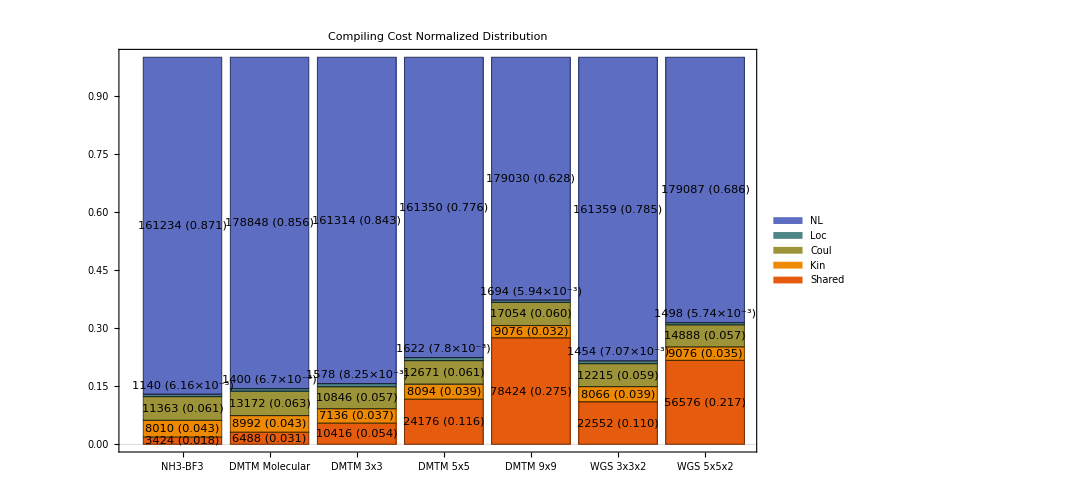

```mathematica
(* Get block encoding data from all instance results we computed before *)
compdataNH3BF3=Instance1Result["compilationCost"];
compdataDMTMSmall=Instance2Result["compilationCost"];
compdataDMTM3=InstanceDMTMClass3Result["compilationCost"];
compdataDMTM5=InstanceDMTMClass5Result["compilationCost"];
compdataDMTM9=InstanceDMTMClass9Result["compilationCost"];
compdataWGS3=InstanceWGSClass3Result["compilationCost"];
compdataWGS5=InstanceWGSClass5Result["compilationCost"];

allcompData={compdataNH3BF3,compdataDMTMSmall,compdataDMTM3,compdataDMTM5,compdataDMTM9,compdataWGS3,compdataWGS5};
breakdownCompData=First/@allcompData;
totalCompData=allcompData[[All,2]];

(* Create figure *)
compilingDistBarChart=BarChart[Normalize[#,Total]&/@breakdownCompData*1.0,
ChartLayout->"Stacked",Axes->False,Frame->True,PlotLabel->"Compiling Cost Normalized Distribution",
ChartLegends->Map[Style[#,14]&,{"Shared","Kin","Coul","Loc","NL"}],
LabelingFunction->(Function[{value,index,barPos},
If[index[[2]]==4,
Placed[Row[{NumberForm[breakdownCompData[[index[[1]],index[[2]]]],{Infinity,1}]," (",ScientificForm[value,3],")"}],Above],Placed[Row[{NumberForm[breakdownCompData[[index[[1]],index[[2]]]],{Infinity,1}]," (",NumberForm[value,{Infinity,3}],")"}],Center]]]),
ChartLabels->{{"NH3-BF3","DMTM Molecular","DMTM 3x3","DMTM 5x5","DMTM 9x9","WGS 3x3x2","WGS 5x5x2"},None},
Epilog->Table[Style[Text[Style[totalCompData[[i]],Black],{i,1.025}],11.5],{i,Length@totalCompData}],
PlotTheme->"Scientific",ImageSize->800,LabelStyle->Directive[FontSize->11.5],FrameStyle->Directive[FontSize->14]]
```

The numbers inside each color bar indicate the values of the cost for that term and in parenthesis, the relative fraction of the total for that term. The total compilation cost (sum of all global values per term) is shown on top of each bar stack. The numbers above the green bar are for the local term. We can see that the non-local terms appear to have the dominating costs across all instances.
@Karthik Maybe we can try to unify the labels between Fig. 6 and Fig 7? What do you think?

### Figure 2: Summary of Total Time Evolution Cost w.r.t. Different Time

Lastly, we combine the rescaling factor cost and the block encoding cost as the total QSP cost.

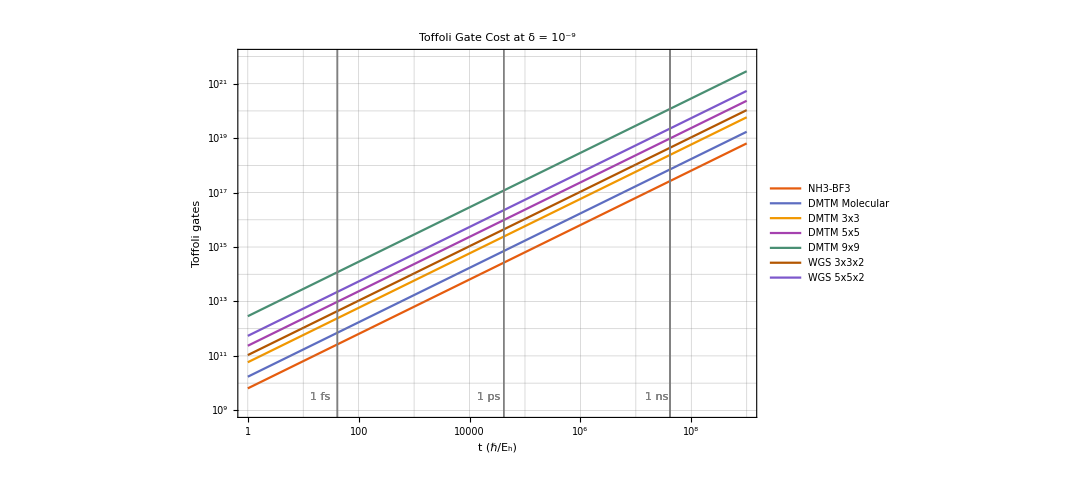

```mathematica
timeLabels={"1 fs", "1 ps", "1 ns"};
timePts={41.34137333517015,41341.373335170145,4.134137333517015*10^7};
timeLabelPts={3,10,17};
δerror=10^-9;
costPlotLine=LogLogPlot[{CostAnalysis`totalCost[Instance1Result,t,δerror,True]["exact"]["total"],CostAnalysis`totalCost[Instance2Result,t,δerror,True]["exact"]["total"],
CostAnalysis`totalCost[InstanceDMTMClass3Result,t,δerror,True]["exact"]["total"],
CostAnalysis`totalCost[InstanceDMTMClass5Result,t,δerror,True]["exact"]["total"],
CostAnalysis`totalCost[InstanceDMTMClass9Result,t,δerror,True]["exact"]["total"],
CostAnalysis`totalCost[InstanceWGSClass3Result,t,δerror,True]["exact"]["total"],
CostAnalysis`totalCost[InstanceWGSClass5Result,t,δerror,True]["exact"]["total"]},
{t,1,10^9},
PlotLegends->Placed[{"NH3-BF3","DMTM Molecular","DMTM 3x3","DMTM 5x5","DMTM 9x9","WGS 3x3x2","WGS 5x5x2"},{0.72,0.25}],
Ticks->{Table[10^i,{i,0,6}],Table[10^i,{i,9,18}] },
Frame->True,FrameLabel->{Row[{"t (",ℏ,"/",Subscript[Style["E",Italic],"h"],")"}],"Toffoli gates"},PlotRange->{{1,10^9},{10^9,10^22}},
GridLines->All,
PlotLabel->"Toffoli Gate Cost at δ = 10^-9",Epilog->{Thick,Gray,Table[{InfiniteLine[{{Log[x],0},{Log[x],1}}],Style[Text[Style[timeLabels[[i]],Gray],{timeLabelPts[[i]],Log@(10^9.5)}],14]},{x,timePts},{i,1,3}]},PlotTheme->"Scientific",ImageSize->800,LabelStyle->Directive[FontSize->14],TicksStyle->Directive[FontSize->14],Exclusions->None]
```

You can also export these figures as pdf files if needed.

```mathematica
(* Export figs *)
(*SetDirectory["..."]
Export["rescalingFactorDist.pdf",rescalingFactorDistBarChart]
Export["compilingDist.pdf",compilingDistBarChart]
Export["timeEvoCost.pdf",costPlotLine]*)
```